```mathematica
(*** DATA-DRIVEN PREDICTIONS for RF detector ***)
```

```mathematica
(** FNR **) 
(* test if data is there *)
```

```mathematica
getMonValues[dataDirPathForSeshNumPostCorr[All], "FPR",11]
```

{0.189048,0.270127,0.342801,0.409231,0.469308,0.523021,0.571181,0.613939,0.652491,0.687322,0.7186,0.746941,0.772036,0.795329,0.816313,0.834639,0.851623,0.866614,0.880062,0.892301,0.903391,0.913582,0.922356,0.930144,0.937203,0.943659,0.949452,0.954618,0.959474,0.963681}

{0.189048,0.270127,0.342801,0.409231,0.469308,0.523021,0.571181,0.613939,0.652491,0.687322,0.7186,0.746941,0.772036,0.795329,0.816313,0.834639,0.851623,0.866614,0.880062,0.892301,0.903391,0.913582,0.922356,0.930144,0.937203,0.943659,0.949452,0.954618,0.959474}

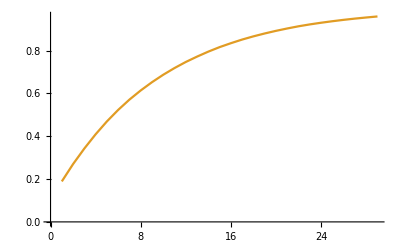

```mathematica
(* EMPIRICAL *) 
(* all sessions 4-7 *) 
getMonValues[dataDirPathForSeshNum[All], "FPR",11]
estRfFNRChartSesh4567 = ListLinePlot[Inner[List, Range[1,29], getMonValues[dataDirPathForSeshNum[All], "FPR",11], List], PlotStyle->{ColorData[97,"ColorList"][[2]](*Darker@Blue,Dotted*)}(*, PlotLegends->{"Data estimate (7.7 hrs)"}*)]
```

```mathematica
(*** APPROACH PREDICTIONS ***)
```

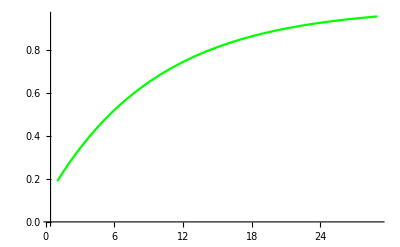

```mathematica
(* updated *) 
gtRfFPRChart =ListLinePlot[ {#, Simplify@predRfMonFPRTheor[0.1, #]}& /@ Table[n, {n,1,29, 1}], 
PlotStyle->Green, (*PlotLegends->{"Ground-truth FPR"},*) PlotRange->All]
```

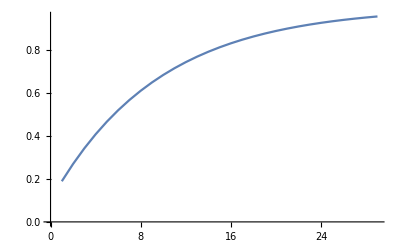

```mathematica
(* automated for sessions 4-7, det fnr = 0.09959699010793902 *) 
predRfFNRchartSesh4567 = ListLinePlot[Inner[List, Range[1,29], predRfMonFPRTheor[countFromFiles[ "FNcount",detFilenames[fullTripleList[{4,5,6,7}]]]/countFromFiles[ "h1count",detFilenames[fullTripleList[{4,5,6,7}]]],#]&/@ Range[1,29], List], PlotStyle->{ColorData[97,"ColorList"][[1]](*Darker@Magenta,Dashed*)}(*, PlotLegends->{"Our prediction (7.7 hrs)"}*)]
```

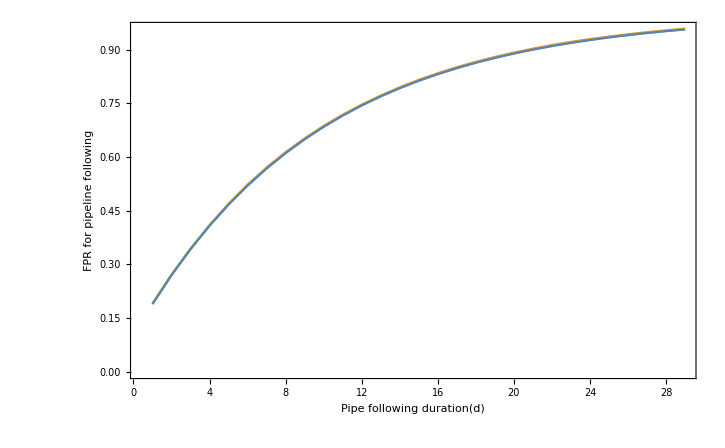

```mathematica
(* POST-CORRECTION *) 
Show[gtRfFPRChart,estRfFNRChartSesh4567, predRfFNRchartSesh4567,(*PlotLabel->"Bhah",  AxesLabel -> {"Monitor window size", "Monitor FPR"}*)Frame->True, FrameLabel->{StringJoin["Pipe following duration", ToString[ Style["(d)", Italic], StandardForm] ],"FPR for pipeline following"}, ImageSize->500, BaseStyle-> {FontSize->15}]
```

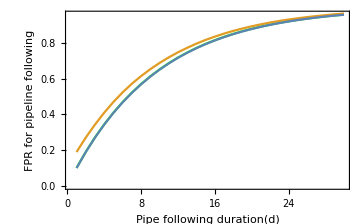
```mathematica
(* old: *)  
-Graphics-
```

```mathematica
(*** CALCULATION OF MSE for that chart ***)

bbcVal = {0.189048,0.270127,0.342801,0.409231,0.469308,0.523021,0.571181,0.613939,0.652491,0.687322,0.7186,0.746941,0.772036,0.795329,0.816313,0.834639,0.851623,0.866614,0.880062,0.892301,0.903391,0.913582,0.922356,0.930144,0.937203,0.943659,0.949452,0.954618,0.959474};
eccVal ={0.18999999999999995,0.2709999999999999,0.3438999999999999,0.4095099999999998,0.46855899999999984,0.5217030999999999,0.5695327899999998,0.6125795109999999,0.6513215598999997,0.6861894039099998,0.7175704635189999,0.7458134171670998,0.7712320754503899,0.794108867905351,0.8146979811148157,0.8332281830033341,0.8499053647030008,0.8649148282327007,0.8784233454094306,0.8905810108684875,0.9015229097816387,0.9113706188034749,0.9202335569231274,0.9282102012308147,0.9353891811077332,0.9418502629969598,0.9476652366972639,0.9528987130275375,0.9576088417247838};
nccVal ={238304688/1259043289,12063055460238/44674633023587,543282712004500320/1585190003575937521,22959400838469143922894/56247296896884991057643,932307844621842237590250768/1995822835792170137698346569,36839541229512766915396878561678/70817781682413572995950431307827,1427256543207352957147703697408911040/2512827347437080810615309154095625441,54479751144774363212626487979091239125454/89162652769109938403063014714775077523003,2055674384210430652596628358446001122785422448/3163758408206327944355884951124364075748715449,76857463115740211875163376841264792515567422187918/112259639598385134449579865720745810499791670276867,2852244655425477094344409972158684550386127334240240160/3983308791869499725674442375369223593964107836434071761,105203377766655379717743033555052648881355539295599442475214/141339745861905458766106238805226160784628438360190168295563,3860637378142846617881591626988046331323305026120018642397131728/5015158202417991393397747671525839863120970878334627741631461929,141067072681630988178966611161813410315717783363543050044871548034958/177952858496397588611932280628751375863121409675947596156309163626707,5135837307031697519484372939750784008477138522476635710699997672425655680/6314301278027675636717193113549985069751136979531648554414318052966444481,186399606838905509750164791515383445523336616740270880312454425635510688116174/224050352248256014617636163248094120229979593444721485656283247473408349519323,6747074983741528886666741125043750321917829451468560085411911441199956081824930608/7949978648824868166677583980532123668120365914199052475541898470098948465994138009,243657523200505190501154293991223304078090106285748477617390227828227080737047991718798/282089092396252797158220712381221344115914943733524978989653183414520988418869998973347,8781517061261297716478530536280829572096544216877655387147434739070944175540232863795685600/10009367265496238001565145537422876953265009948496666829489863907097448232066764173571271601,315933792506500905841303796432888671151751036343011432539390571526259977516458844354809233072334/355162378681603013009536059104375942932702348002507229110788841015538755618424993170829430218283,11348912583050982488699515425109224736951463957963732805878517133841393984028857544157511393819411088/12602226682759319710617367985200571583081077414172964010538120445754361665608574032680540672435335689,407122677212767275388782596776513441095470849574670554228254461564394610521998670309781362257522841175438/447164809384348941291836068218871881482465869887099281985924127776702014980789032401603624680023016252787,14587442850634990839921563849498321158718232557242158399576757660083708332509443958234471952384798592151417920/15866748931384853483858219208610230970642336461203943822706545825900717597563337236706101414521256685697641121,522127302358451394556608990110850418950138829025224456177522763430747533505133058816152506805660051347901114847694/562999852332328756167741192179116825531302024652899538661096365540435162514339895170042596491457750978609399896443,18671086661192613428985897998212558896465606803650243120043989324668850812281173285648186975934844672472498337503005168/19976923760308021255099960722091602320327189740758834330311682338471260871496322500318621451306395377973997336525486969,667120996307371353558193716336764766783215960313663337965606900318002550521439209019299933903059153706583955972164583060878/708841185787009518194711906301976325132169673571345718542449424415975749503304011278805644956704827196651347491933854121027,23818893461595499012130842920114481866974054342462365753992191124145921785354137664816912737545831761084616671391180504675700640/25151811795280458734102962571313025944664776527332060131041732926552067519625736232205860699998757383418779763056288945776401041,849876330089035739104888170181757814856399382434921623977397998387773061734636696097851056765647387527894385716917751078257761026254/892461737931936517262175420917900099594540265519323489629753809432847011798879998727360555218055908235848562332526300662984038137803,30306658651866066480666600086660839378814209167758600176805438613026642889057149719132735614746277963834186548552953175742242797806784848/31667219847038903442013770460429849233913072241422155382532554420105710519659658994842934580802277791932614537245030726424662625243663849};
```

```mathematica
Mean@((eccVal-nccVal)^2)
```

1.41298×10^-6

```mathematica
Sqrt@Mean@((eccVal-nccVal)^2)
```

0.00118869

```mathematica
Mean@((eccVal-bbcVal)^2)
```

2.26987×10^-6

```mathematica
Sqrt@Mean@((eccVal-bbcVal)^2)
```

0.00150661

```mathematica
Max@Abs[eccVal-nccVal]
```

0.0208064

```mathematica
Max@Abs[eccVal-bbcVal]
```

0.0299768